# 9. NALOGA: MINECRAFT PRAVLJICA

## REŠITEV

```mathematica
Remove["Global`*"];

pravljica = Import[NotebookDirectory[]<>"pravljica.txt"];


SmerNPredjiStr=StringReplace[
	StringSplit[pravljica,"."][[3;;-3]],
	(__~~" in "~~SmerNPred__~~"prej"~~__)->SmerNPred
];

SmerNPredji=(StringSplit/@SmerNPredjiStr)/.{
	{a_}->{a,""},
	{a_,"od"}->{a,""},
	{a_,"od",b_}->{a,b}
};

{premiki,NPredji}=Transpose[
	{#1,(StringLength@#2)/4}&@@@(SmerNPredji/.Thread[
		{"levo","desno","zadaj","spredaj","pod","nad"}->
		{{-1,0,0},{1,0,0},{0,-1,0},{0,1,0},{0,0,-1},{0,0,1}}
	])
];


indr=1;
rAssI=<|1->{0,0,0}|>;
Do[
	rAssI[i+1]=rAssI[i-NPredji[[i]]]+premiki[[i]],
{i,Length@premiki}];

rji=Values@rAssI;
Length@DeleteDuplicates@rji[[;;,;;2]]
```

1785

## ZA PREDSTAVO

To je skulptura, ki so jo postavili:

```mathematica
Show[Graphics3D[{
	EdgeForm[], FaceForm[RGBColor@{0,.7,1}],
	Cuboid[#,#+{1,1,1}]
}]&/@rji,
Lighting->"Neutral"
]
```

-Graphics3D-

To je pa tloris

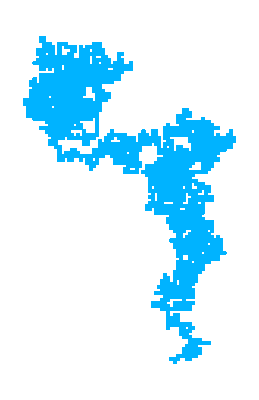

```mathematica
Show[Graphics[{
	EdgeForm[], FaceForm[RGBColor@{0,.7,1}],
	Rectangle[#,#+{1,1}]
}]&/@(DeleteDuplicates@rji[[;;,;;2]])
]
```